```mathematica
Needs["NumericalCalculus`"];
Needs["ColorBar`"];
```

## Set up

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);
Ic1=Quantity[5*10^-6,"Ampere"];
EJ=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
EL=2.5EJ
(*EJ2=α EJ1*)
(*EL=β EJ1*)
```

2618.942

6547.36

```mathematica
Table
```

```mathematica
Clear[precomputeElement2,h2]
```

## 2 JJs/Arm

### Precompute joint element

```mathematica
precomputeElement2[EJ_]:=Module[{t1,ϕ,ϕ0,ϕm1,int1,fm,res,sres},
t1=Monitor[Table[
res=Table[
(fm=FindMinimum[-EJ Cos[ϕm1-ϕ0]-EJ Cos[ϕ-ϕm1], {ϕm1, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1-2π,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ0,ϕ, sres[[1,1]],Mod[sres[[1,2]],2π]}
,{ϕ0,0,4.π,π/50.},{ϕ,0,4.π,π/50.}],{ϕ,ϕ0}];
(*Return[Interpolation[t1]];*)
Return[Flatten[t1,1]];
];
```

### Middle phase1

```mathematica
h2=Quiet[precomputeElement2[EJ]]
```

{{0.,0.,-5237.88,6.46915×10^-10},{0.,0.0628319,-5235.3,0.0314159},{0.,0.125664,-5227.55,0.0628319},{0.,0.188496,-5214.64,0.0942478},40394,{12.5664,12.4407,-5227.55,6.22035},{12.5664,12.5035,-5235.3,6.25177},{12.5664,12.5664,-5237.88,6.46915×10^-10}}
 |  |  |  |

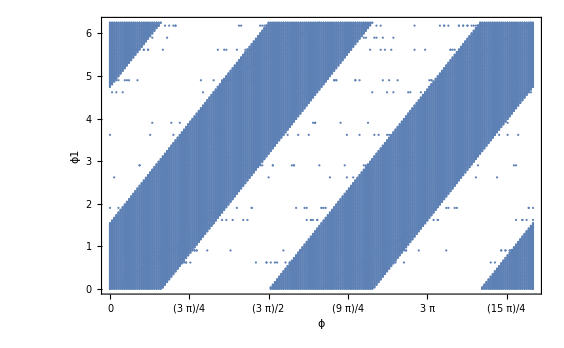

```mathematica
midphase1=Table[{h2[[i,1]],h2[[i,4]]},{i,1,Length[h2]}];
ListPlot[midphase1,Frame->True, FrameLabel->{"ϕ","ϕ1"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}}]
```

```mathematica
Earm1=Table[{h2[[i,1]],h2[[i,2]],h2[[i,3]]},{i,1,Length[h2]}]
ListPlot3D[]
```

{{0.,0.,-5237.88},{0.,0.0628319,-5235.3},{0.,0.125664,-5227.55},{0.,0.188496,-5214.64},{0.,0.251327,-5196.58},40391,{12.5664,12.315,-5196.58},{12.5664,12.3779,-5214.64},{12.5664,12.4407,-5227.55},{12.5664,12.5035,-5235.3},{12.5664,12.5664,-5237.88}}
 |  |  |  |

Plot3D

### Hamiltonian(2 JJs)

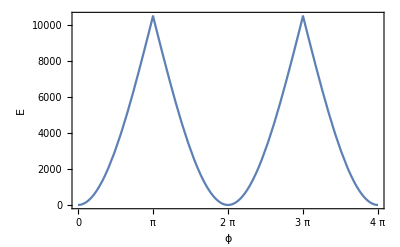

```mathematica
hm2=Interpolation[Table[{h2[[i,1]],2(h2[[i,2]]-h2[[1,2]])},{i,1,Length[h2]}]];
Plot[hm2[x],{x,0π,4π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}}]
```

## 3 JJs/Arm

### Precompute joint element

```mathematica
precomputeElement3[EJ_]:=Module[{t1,ϕ,ϕm1,ϕm2,int1,fm,res,sres},
ϕm1[ϕm2_]:=1/2 Mod[ϕm2,2π]+π UnitStep[Mod[ϕm2,2π]-Pi];
t1=Monitor[Table[
res=Table[
(fm=FindMinimum[-EJ Cos[ϕm1[ϕm2]]-EJ Cos[ϕm2-ϕm1[ϕm2]]-EJ Cos[ϕ-ϕm2], {ϕm2, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]],2π]}
,{ϕ,0,4.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase2

```mathematica
h3=Quiet[precomputeElement3[EJ]];
```

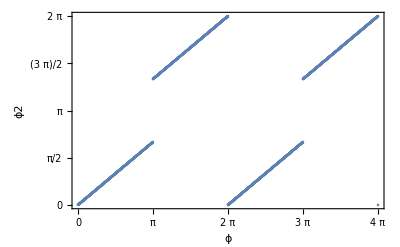

```mathematica
midphase2=Table[{h3[[i,1]],h3[[i,3]]},{i,1,Length[h3]}];
ListPlot[midphase2,Frame->True, FrameLabel->{"ϕ","ϕ2"}, FrameTicks->{{π Range[0,2,1/4],None},{π Range[0,4,1/4],None}}]
```

### Hamiltonian(3 JJs)

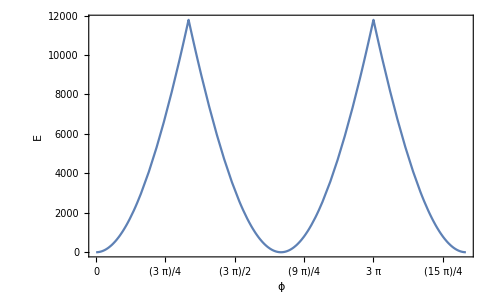

```mathematica
hm3=Interpolation[Table[{h3[[i,1]],3(h3[[i,2]]-h3[[1,2]])},{i,1,Length[h3]}]];
Plot[hm3[x],{x,0,4π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}}]
```

## 4 JJs/Arm

### Precompute joint element

```mathematica
precomputeElement4[EJ_]:=Module[{t1,ϕ,ϕm1,ϕm2,ϕm3,int1,fm,res,sres},
ϕm1[ϕm2_]:=1/2 Mod[ϕm2,2π]+π UnitStep[Mod[ϕm2,2π]-Pi];
ϕm2[ϕm3_]:=2/3 Mod[ϕm3,2π]+2/3 π UnitStep[Mod[ϕm3,2π]-Pi];
t1=Monitor[Table[
res=Table[
(fm=FindMinimum[-EJ Cos[ϕm1[ϕm2[ϕm3]]]-EJ Cos[ϕm2[ϕm3]-ϕm1[ϕm2[ϕm3]]]-EJ Cos[ϕm3-ϕm2[ϕm3]]-EJ Cos[ϕ-ϕm3], {ϕm3, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]],2π]}
,{ϕ,0,2.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase3

```mathematica
h4=Quiet[precomputeElement4[EJ]];
```

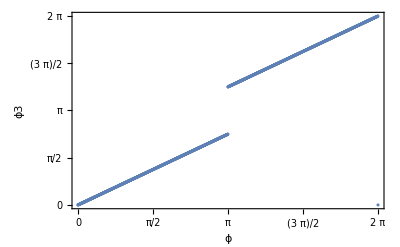

```mathematica
midphase3=Table[{h4[[i,1]],h4[[i,3]]},{i,1,Length[h4]}];
ListPlot[midphase3,Frame->True, FrameLabel->{"ϕ","ϕ3"}, FrameTicks->{{π Range[0,2,1/4],None},{π Range[0,2,1/4],None}}]
```

### Hamiltonian(4 JJs)

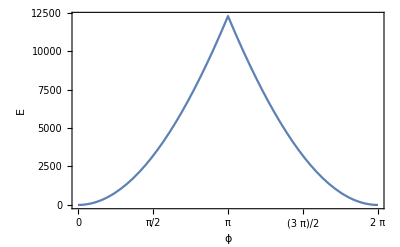

```mathematica
hm4=Interpolation[Table[{h4[[i,1]],4(h4[[i,2]]-h4[[1,2]])},{i,1,Length[h4]}]];
Plot[hm4[x],{x,0,2π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[0,2,1/4],None}}]
```

## 5 JJs/Arm

### Precompute joint element

```mathematica
precomputeElement5[EJ_]:=Module[{t1,ϕ,ϕm1,ϕm2,ϕm3,ϕm4,int1,fm,res,sres},
ϕm1[ϕm2_]:=1/2 Mod[ϕm2,2π]+π UnitStep[Mod[ϕm2,2π]-Pi];
ϕm2[ϕm3_]:=2/3 Mod[ϕm3,2π]+2/3 π UnitStep[Mod[ϕm3,2π]-Pi];
ϕm3[ϕm4_]:=3/4 Mod[ϕm4,2π]+1/2 π UnitStep[Mod[ϕm4,2π]-Pi];
t1=Monitor[Table[
res=Table[
(fm=FindMinimum[-EJ Cos[ϕm1[ϕm2[ϕm3[ϕm4]]]]-EJ Cos[ϕm2[ϕm3[ϕm4]]-ϕm1[ϕm2[ϕm3[ϕm4]]]]-EJ Cos[ϕm3[ϕm4]-ϕm2[ϕm3[ϕm4]]]-EJ Cos[ϕm4-ϕm3[ϕm4]]-EJ Cos[ϕ-ϕm4], {ϕm4, s1}]);
{fm[[1]],fm[[2,1,2]]}
,{s1,-0.1,2π,1}];
sres=Sort[res,#1[[1]]<#2[[1]]&];
{ϕ, sres[[1,1]],Mod[sres[[1,2]],2π]}
,{ϕ,0,2.π,π/1000.}],ϕ];
(*Return[Interpolation[t1]];*)
Return[t1];
];
```

### Middle phase4

```mathematica
h5=Quiet[precomputeElement5[EJ]];
```

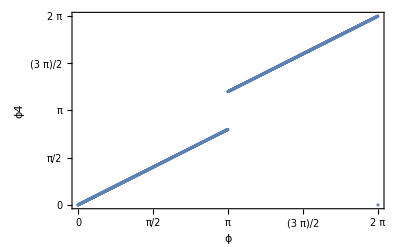

```mathematica
midphase4=Table[{h5[[i,1]],h5[[i,3]]},{i,1,Length[h5]}];
ListPlot[midphase4,Frame->True, FrameLabel->{"ϕ","ϕ4"}, FrameTicks->{{π Range[0,2,1/4],None},{π Range[0,2,1/4],None}}]
```

### Hamiltonian(5 JJs)

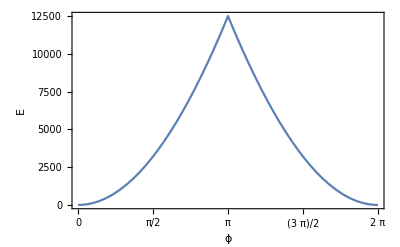

```mathematica
hm5=Interpolation[Table[{h5[[i,1]],5(h5[[i,2]]-h5[[1,2]])},{i,1,Length[h5]}]];
Plot[hm5[x],{x,0,2π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[0,2,1/4],None}}]
```

## Altogether

### get energy functions

```mathematica
getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ,2π]]];
];
getEnergyJJ[EJ_, ϕ_]:=Module[{},
Return[-EJ*Cos[ϕ]];
];
getEnergyLinInd[EL_, ϕ_]:=Module[{},
Return[EL/2 ϕ^2];
];
```

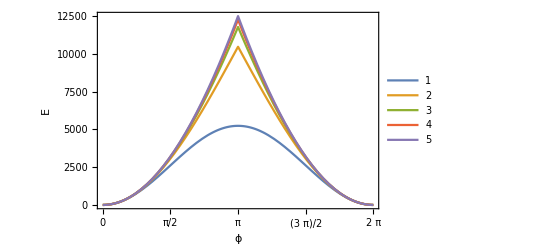

```mathematica
hm1[x_]:=-EJ (Cos[x]-1);
hmlist={hm1,hm2,hm3,hm4,hm5};
Plot[Evaluate[Table[hmlist[[i]][x],{i,1,Length[hmlist]}]],{x,0,2π},Frame->True, FrameLabel->{"ϕ","E"}, FrameTicks->{Automatic,{π Range[0,2,1/4],None}},PlotLegends->{"1","2","3","4","5"}]
```

## Total Hamiltonian

```mathematica
Clear[H]
H[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕext_,Harm_,EL_]:=
(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4])+(getEnergyLinInd[EL,ϕ1-ϕ5]+getEnergyLinInd[EL,ϕ2-ϕ5]+getEnergyLinInd[EL,ϕ3-ϕ5]+getEnergyLinInd[EL,ϕ4-ϕ5]);
Hn[ϕ1_?NumericQ,ϕ2_?NumericQ,ϕ3_?NumericQ,ϕ4_?NumericQ,ϕ5_?NumericQ,ϕext_?NumericQ,Harm_,EL_?NumericQ]:=(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4])+(getEnergyLinInd[EL,ϕ1-ϕ5]+getEnergyLinInd[EL,ϕ2-ϕ5]+getEnergyLinInd[EL,ϕ3-ϕ5]+getEnergyLinInd[EL,ϕ4-ϕ5]);
```

### Find minimum energy of the whole thing

```mathematica
ip=Table[RandomReal[{0,4π},5],50];
Monitor[For[listEmin={};j=1,j≤1,j++,
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[Hn[ϕ1,ϕ2,ϕ3,ϕ4,0,ϕext,hmlist[[j]],EL],{ϕ1,ip[[i,1]]},{ϕ2,ip[[i,2]]},{ϕ3,ip[[i,3]]},{ϕ4,ip[[i,4]]}]];
{res[[1]],ϕ1,ϕ2,ϕ3,ϕ4}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π,π/2}]
,ϕext];
listEmin=Insert[listEmin,t1,1]
],
j]
```

```mathematica
Export["Emin w dif JJ#.txt",listEmin];
```

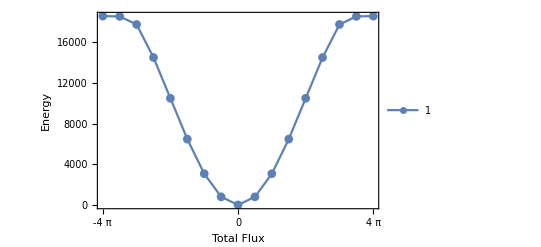

```mathematica
ListPlot[
Table[listEmin[[i,All,1,{1,2}]],{i,1,Length[listEmin]}],Joined->True,
 PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLegends->{"1","2","3","4","5"}
]
```

Find Derivatives

```mathematica
Monitor[
For[listd={};j=1,j<=Length[listEmin],j++,
Monitor[
t2=Table[
{ϕext,ϕ1,ϕ2,ϕ3,ϕ4}=listEmin[[j,i,1,{1,3,4,5,6}]];
ϕf=0;

h00=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ1,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ2,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ3,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ4,-a ϕw+ϕf, ϕext,hmlist[[j]],EJ];
{ϕext,
(ND[h00/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[ND[ND[h00/.{a->1,ϕw->0},{ϕx,1},0],{ϕy,1},0],{ϕz,1},0]),
(*xyzvalue,*)
(ND[ND[h00/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[h00/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24
}
,{i,Length[listEmin[[j]]]}]
,listEmin[[j,i,1,1]]];
listd=Insert[listd,t2,j]]
,j]
```

```mathematica
Export["Derivatives w dif JJ#.txt",listd];
```

```mathematica
x2α=Table[Interpolation[listd[[i,All,{1,2}]]],{i,1,Length[hmlist]}];
xyzα=Table[Interpolation[listd[[i,All,{1,3}]]],{i,1,Length[hmlist]}];x2y2α=Table[Interpolation[listd[[i,All,{1,4}]]],{i,1,Length[hmlist]}];x4α=Table[Interpolation[listd[[i,All,{1,5}]]],{i,1,Length[hmlist]}];
```

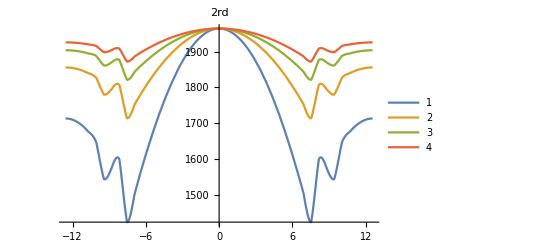

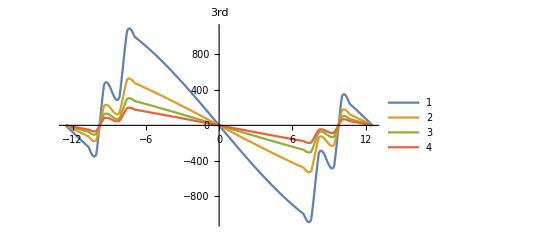

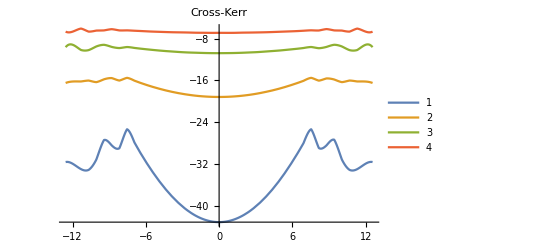

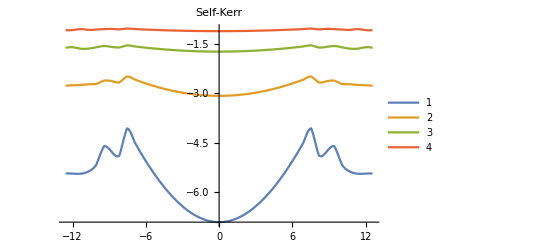

```mathematica
Plot[Evaluate[Table[x2α[[i]][x],{i,2,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"2rd",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[xyzα[[i]][x],{i,2,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"3rd",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[x2y2α[[i]][x],{i,2,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"Cross-Kerr",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
Plot[Evaluate[Table[x4α[[i]][x],{i,2,Length[hmlist]}]],{x,-4π,4π},PlotLabel->"Self-Kerr",PlotLegends->{"1","2","3","4","5"},PlotRange->All]
```

### Phase Diagram α

```mathematica
lenϕ=Length[Table[i,{i,-4Pi,4Pi,Pi/5}]];
lenα=Length[αlist];
```

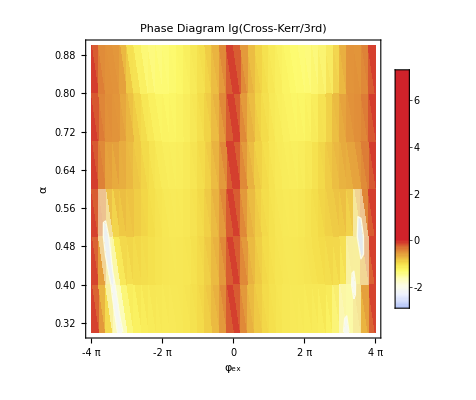

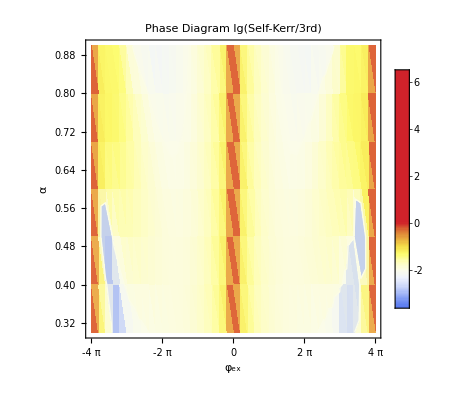

```mathematica
tableαcrossvs3rd=Flatten[Table[{listt2[[j,i,1]],αlist[[j]],Log10[Abs[listt2[[j,i,4]]/listt2[[j,i,3]]]]},{i,1,lenϕ},{j,1,lenα}],1];
tableαselfvs3rd=Flatten[Table[{listt2[[j,i,1]],αlist[[j]],Log10[Abs[listt2[[j,i,5]]/listt2[[j,i,3]]]]},{i,1,lenϕ},{j,1,lenα}],1];

ListDensityPlot[
tableαcrossvs3rd,
PlotLegends->Automatic,FrameLabel->{"φ_ex","α"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{1/2π Range[-8,8],None}},FrameTicksStyle->Directive[6],PlotLabel->Style["Phase Diagram lg(Cross-Kerr/3rd)",14],PlotRange->All,Mesh->1,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]

ListDensityPlot[
tableαselfvs3rd,
PlotLegends->Automatic,FrameLabel->{"φ_ex","α"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{1/2π Range[-8,8],None}},FrameTicksStyle->Directive[6],PlotLabel->Style["Phase Diagram lg(Self-Kerr/3rd)",14],PlotRange->All,Mesh->1,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},ColorFunction->(ColorData[{"TemperatureMap",{-4,0}}]),ColorFunctionScaling->False
]
```